# Контролна работа №1 Група Б, задача 1 Фак. №2001261051

## Дадено е уравнението: 3 x^3 - (2b + 40)sin2x - 6(a + b - 1) = 0

```mathematica
f[x_] := 3 x^3-42Sin[2x]-30
```

```mathematica
f[x]
```

-30+3 x^3-42 Sin[2 x]

### 1. Да се намери броят на корените на уравнението

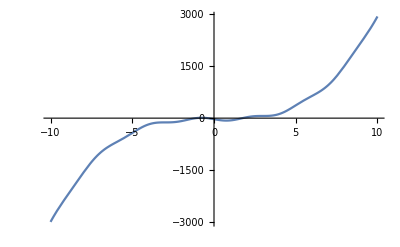

```mathematica
Plot[f[x], {x, -10, 10}]
```

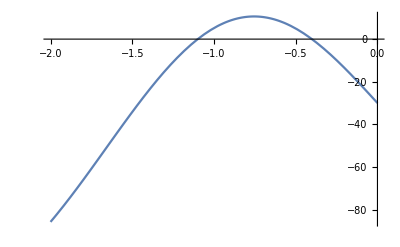

```mathematica
Plot[f[x], {x, -2, 0}]
```

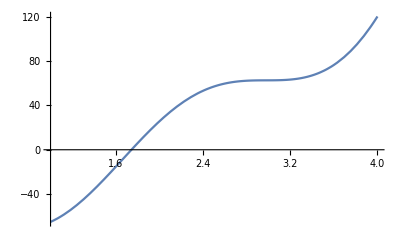

```mathematica
Plot[f[x], {x, 1, 4}]
```

Брой корени: 3

### 2. Да се локализира най-малкият от тях (в случай на повече от един) в интервал [p, q].

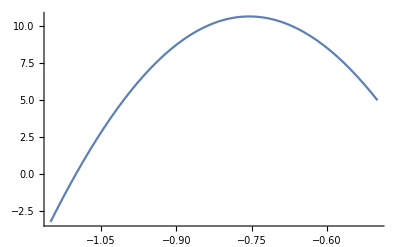

```mathematica
Plot[f[x], {x, -1.15, -0.5}]
```

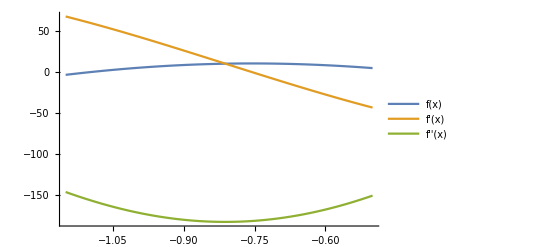

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -1.15, -0.5}, PlotLegends->"Expressions"]
```

```mathematica
f[-1.15]
```

-3.24301

```mathematica
f[-0.5]
```

4.96678

Извод:
1. f(-1.15) = -3.24301 < 0 
2. f(-0.5) = 4.96678 > 0
Следователно в двата края на функцията има различни знаци и функцията е непрекъсната в избрания интервал [-1.15; -0.5]. 
Следва, че функцията има поне един корен в дадения интервал.

### 3. Да се определи началното приближение за метода на допирателните

```mathematica
f[-1.15]
```

-3.24301

```mathematica
f[-0.5]
```

4.96678

f’’ < 0 за текущата задача. Следователно избираме x0 така, че f(x_0).f’’ > 0.
=> f(x_0) < 0
=> x_0 = 2

### 4. Да се проверят условията на метода на допирателните

#### Проверка на първата производна

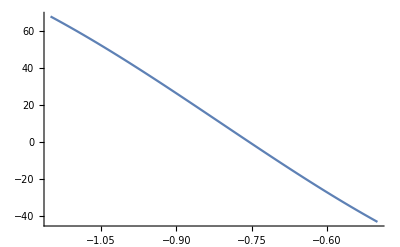

```mathematica
Plot[f'[x], {x, -1.15, -0.5}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [-1.15; -0.5] са между 80 и -60. 
Следователно първата f'(x) > 0 в целия разглеждан интервал [-1.15; -0.5].

#### Проверка на втората производна

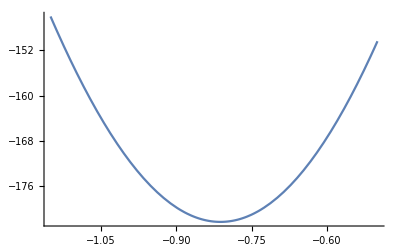

```mathematica
Plot[f''[x], {x, -1.15, -0.5}]
```

Извод: (2) Стойностите на втората производна в разглеждания интервал [-1.15; -0.5] са между -74 и -128. Следователно втората f''(x) < 0 в целия разглеждан интервал [-1.15; -0.5].

Извод: от (1) и (2) следва, че f'(x) и f''(x) са с постоянни знаци в разглеждания интервал [-1.15; -0.5] => Методът на допирателните е сходящ.

#### Пресмятане на постоянните величини:

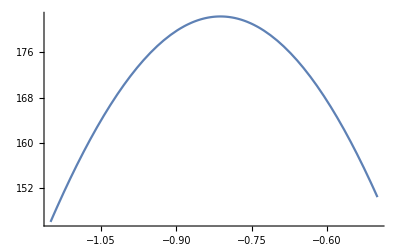

```mathematica
Plot[Abs[f''[x]], {x, -1.15, -0.5}]
```

От геометрични съображения максимума се достига в десния край на интервала, а минимума - в левия.

```mathematica
М2 = Abs[f''[-1.15]]
```

145.978

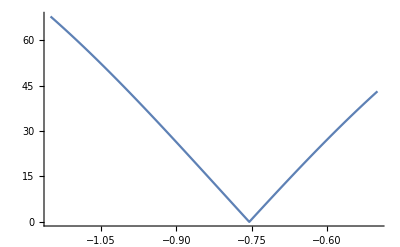

```mathematica
Plot[Abs[f'[x]], {x, -1.15, -0.5}]
```

От геометрични съображения максимума се достига в левия край на интервала, а минимума - в десния.

```mathematica
m1 = Abs[f'[-1.15]]
```

67.8697

```mathematica
p = М2/(2m1)
```

1.07543

### 5. Да се направят 3 итерации по метода на допирателните

???

### 6. Каква е грешката на полученото решение и колко е то?

???

### 7.Колко итерации са необходими за достигане наточност 10^-6?

```mathematica
f[x_] := 3 x^3-42Sin[2x]-30
x0 = 2;
М2 = Abs[f''[2.5]];
m1 = Abs[f'[2.5]];
p = М2/(2m1);
epszad = 0.000001;
eps = 1;
Print["n = ",0,  " x_n = ", N[x0], " f(x) = ", N[f[x0]], " f'(x) = ", N[f'[x0]]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/f'[x0];
Print["n = ",n,  " x_n = ", N[x1], " f(x_n) = ", N[f[x1]] " f'(x_n) = ", N[f'[x1]], " ε_n = ", N[eps = p* (x1 - x0)^2]];
x0 = x1
]
```

n = 0 x_n = 2. f(x) = 25.7857 f'(x) = 90.9061

n = 1 x_n = 1.71635 f(x_n) = -2.77732  f'(x_n) = 106.979 ε_n = 0.144055

n = 2 x_n = 1.74231 f(x_n) = -0.00672028  f'(x_n) = 106.427 ε_n = 0.00120673

n = 3 x_n = 1.74237 f(x_n) = -5.01384×10^-8  f'(x_n) = 106.425 ε_n = 7.13879×10^-9

### 8. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [p, q] за същата точност

```mathematica
Log2[(-1.15 - (-0.5))/0.000001] - 1
```

18.3101+4.53236 ⅈ

### 9. Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на допирателните (Нютон) биха били необходими 3 итерации за достигане на исканата точност. А по метода на разполовяването са необходими доста повече. Следователно методът на допирателните е по-ефективен за избрания интервал [-1.15, -0.5].